```mathematica
g=9.8; (*grav. constant*)
V = 30.;
th = 50. * π/ 180.;
y0=1.; (*20 degrees*)
yprime0 = V Sin[th]; (*starting from rest*)
x0 = 1.;
xprime0=V Cos[th];
vt = 100.;
ode1={x''[t] == (-g x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t] ^ 2]};
ode2 ={y''[t]==-g (1+(y'[t] / vt ^ 2) Sqrt[x'[t]^2+y'[t]^2])};
sol=NDSolve[{ode1, ode2,y[0]==y0, y'[0]==yprime0,x[0]==x0,x'[0]==xprime0},{y, x},{t,0,200}]
```

{{y→InterpolatingFunction[{{0.,200.}},<>],x→InterpolatingFunction[{{0.,200.}},<>]}}

```mathematica
myplot1 = ParametricPlot[ Evaluate[{x[t],y[t]}/.sol],{t,0,200},PlotStyle-> RGBColor[0,0,1],PlotRange-> {{0,100},{0,100}}];
```

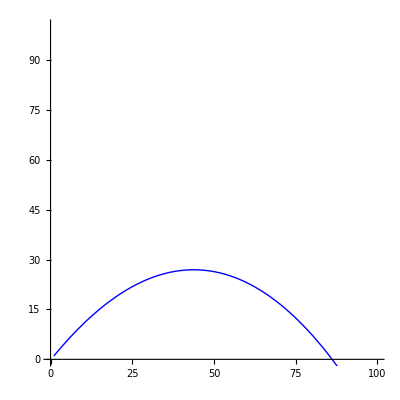

```mathematica
Show[{myplot1}]
```

```mathematica
Manipulate[
Module[
{result = NDSolve[{x''[t] == (-g x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t] ^ 2],y''[t]==-g (1+(y'[t] / vt ^ 2) Sqrt[x'[t]^2+y'[t]^2]),y[0]==y0, y'[0]==yprime0,x[0]==x0,x'[0]==xprime0},{y, x},{t,0,200}]},
ParametricPlot[ Evaluate[{x[t],y[t]}/.sol],{t,0,200},PlotStyle-> RGBColor[0,0,1],PlotRange-> {{0,100},{0,100}},AxesLabel->{"x (m)","y (m)"},PlotRange->{{0,200},{0,200}},ImageSize->{500,300}]],
{{vt,0.5,"terminal velocity (m/s)"},0,2,Appearance->"Labeled"},

{{yprime0,0,"initial velocity (m/s)"},0.,10.,Appearance->"Labeled"},
{{th, 45 * Pi /180, "angle (rad)"}, 0., Pi, Appearance -> "Labeled"}]
```